```mathematica
(* General bulk-service CTMC with capacity cap = k N, where k may be real
   but k N must be an integer. Service removes up to N items. *)

ClearAll[bulkServiceQCapNoBlock];

bulkServiceQCapNoBlock[λ_?NumericQ, μ_?NumericQ, N_Integer?Positive, k_?NumericQ] :=
 Module[{cap = k N, nStates, Q, i, to},
  
  If[! PossibleZeroQ[cap - Round[cap]],
   Message[bulkServiceQCapNoBlock::badcap, k, N, cap];
   Return[$Failed]
  ];
  
  cap = Round[cap];
  nStates = cap + 1;
  
  Q = ConstantArray[0.0, {nStates, nStates}];
  
  For[i = 0, i <= cap, i++,
   
   If[i < cap,
    Q[[i + 1, i + 2]] = λ;
   ];
   
   If[i > 0,
    to = Max[0, i - N];
    Q[[i + 1, to + 1]] = μ;
   ];
  ];
  
  Do[
   Q[[r, r]] = -Total[Q[[r, All]]] + Q[[r, r]],
   {r, 1, nStates}
  ];
  
  Q
 ]

bulkServiceQCapNoBlock::badcap =
  "k = `1` and N = `2` give k N = `3`, which is not an integer.";
```

```mathematica
(* --- Stationary distribution for a CTMC generator Q --- *)
ClearAll[stationaryDist];

stationaryDist[Q_?MatrixQ] :=
 Module[{n = Length[Q], A, b},
  (* Solve π.Q = 0 plus normalization Sum[π]=1 *)
  A = Join[Transpose[Q], {ConstantArray[1.0, n]}];
  b = Join[ConstantArray[0.0, n], {1.0}];
  LinearSolve[A, b]
 ]
```

```mathematica
ClearAll[bulkServiceResultsCap];

bulkServiceResultsCap[lambdaVals_List, N_Integer?Positive, k_?NumericQ] :=
 Module[{cap = k N, nSections, sectionRanges},
  
  If[! PossibleZeroQ[cap - Round[cap]],
   Message[bulkServiceResultsCap::badcap, k, N, cap];
   Return[$Failed]
  ];
  
  cap = Round[cap];
  nSections = Ceiling[cap/N];
  
  sectionRanges = Table[
    {(j - 1) N, Min[j N - 1, cap - 1]},
    {j, 1, nSections}
   ];
  
  Table[
   Module[{μ = 1.0/N, Q, π, pBlock, pSecs, pSecsAcc},
    
    Q = bulkServiceQCapNoBlock[λ, μ, N, k];
    π = stationaryDist[Q];
    
    pBlock = π[[cap + 1]];
    
    pSecs = Table[
      If[range[[1]] <= range[[2]],
       Total[π[[range[[1]] + 1 ;; range[[2]] + 1]]],
       0
      ],
      {range, sectionRanges}
    ];
    
    pSecsAcc = pSecs/(1 - pBlock);
    
    Association[
     Join[
      {
       "lambda" -> λ,
       "mu" -> μ,
       "capacity" -> cap,
       "k" -> k,
       "P(Block)" -> pBlock
      },
      Table[
       "P(Sec" <> ToString[j] <> " | Acc)" -> pSecsAcc[[j]],
       {j, 1, nSections}
      ],
      Table[
       "P(Sec" <> ToString[j] <> ")" -> pSecs[[j]],
       {j, 1, nSections}
      ]
     ]
    ]
   ],
   {λ, lambdaVals}
  ]
 ]

bulkServiceResultsCap::badcap =
  "k = `1` and N = `2` give k N = `3`, which is not an integer.";
```

```mathematica
ClearAll[closedFormResultsCap];

closedFormResultsCap[lambdaVals_List, N_Integer?Positive, k_?NumericQ] :=
 Module[{cap = k N, nSections, sectionRanges},
  
  If[! PossibleZeroQ[cap - Round[cap]],
   Message[closedFormResultsCap::badcap, k, N, cap];
   Return[$Failed]
  ];
  
  cap = Round[cap];
  nSections = Ceiling[cap/N];
  
  sectionRanges = Table[
    {(j - 1) N, Min[j N - 1, cap - 1]},
    {j, 1, nSections}
   ];
  
  Table[
   Module[{μ = 1.0/N, π, eqns, vars, sol, pBlock, pSecs, pSecsAcc},
    
    vars = Array[π, cap + 1, 0];
    
    eqns = Join[
      {
       λ π[0] == μ Sum[π[j], {j, 1, Min[N, cap]}]
      },
      Table[
       (λ + μ) π[i] == λ π[i - 1] + μ π[i + N],
       {i, 1, cap - N}
      ],
      Table[
       (λ + μ) π[i] == λ π[i - 1],
       {i, cap - N + 1, cap - 1}
      ],
      {
       μ π[cap] == λ π[cap - 1],
       Sum[π[i], {i, 0, cap}] == 1
      }
     ];
    
    sol = Solve[eqns, vars][[1]];
    π = vars /. sol;
    
    pBlock = π[[cap + 1]];
    
    pSecs = Table[
      If[range[[1]] <= range[[2]],
       Total[π[[range[[1]] + 1 ;; range[[2]] + 1]]],
       0
      ],
      {range, sectionRanges}
    ];
    
    pSecsAcc = pSecs/(1 - pBlock);
    
    Association[
     Join[
      {
       "lambda" -> λ,
       "mu" -> μ,
       "capacity" -> cap,
       "k" -> k,
       "P(Block)" -> pBlock
      },
      Table[
       "P(Sec" <> ToString[j] <> " | Acc)" -> pSecs[[j]],
       {j, 1, nSections}
      ],
      Table[
       "P{Sec" <> ToString[j] <> ")" -> pSecsAcc[[j]],
       {j, 1, nSections}
      ]
     ]
    ]
   ],
   {λ, lambdaVals}
  ]
 ]

closedFormResultsCap::badcap =
  "k = `1` and N = `2` give k N = `3`, which is not an integer.";
```

{0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

k = 0.5

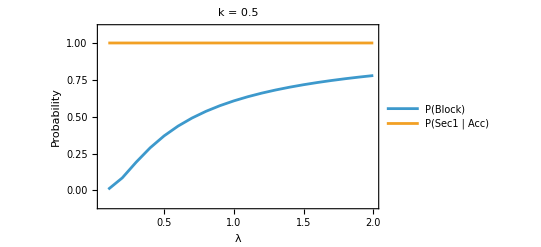

k = 1.

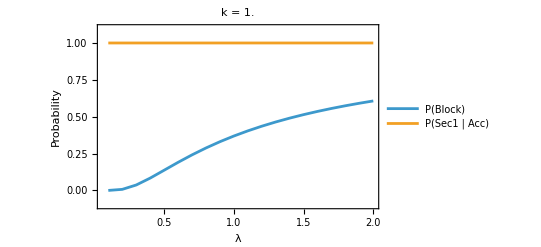

k = 1.5

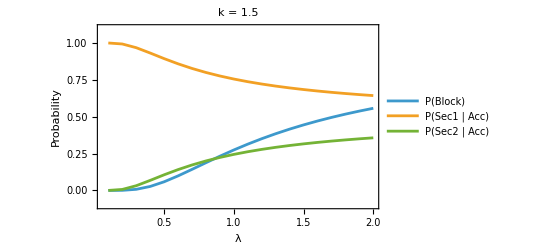

k = 2.

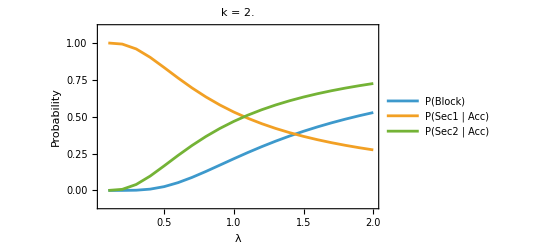

k = 2.5

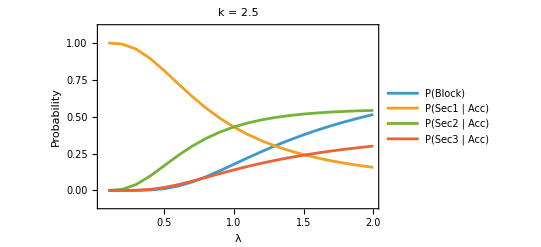

k = 3.

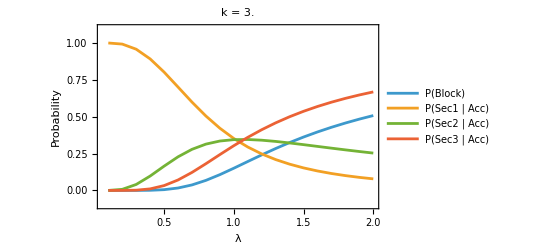

k = 3.5

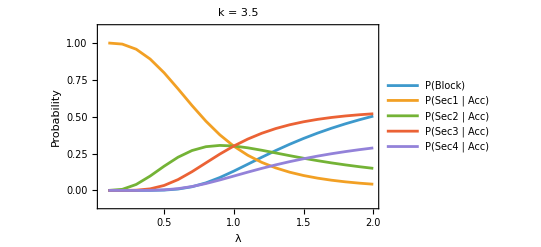

k = 4.

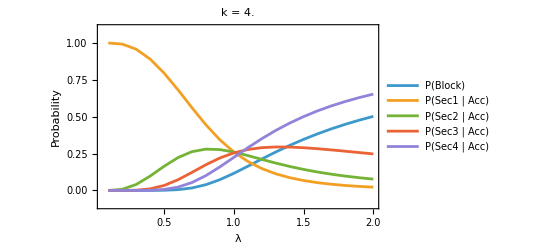

k = 4.5

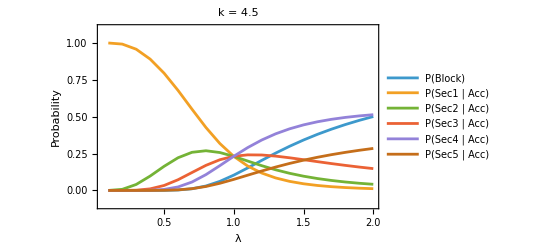

k = 5.

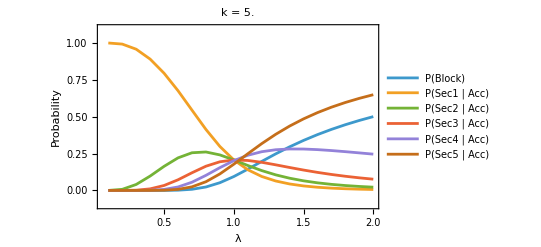

k = 5.5

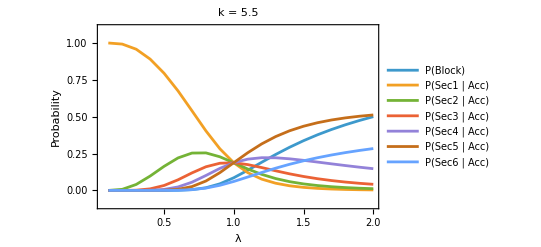

k = 6.

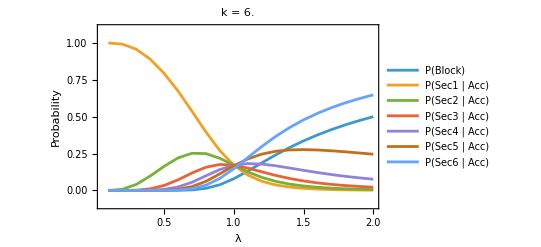

k = 6.5

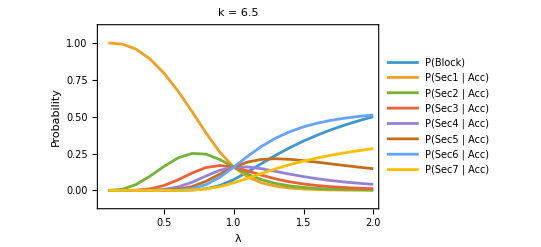

k = 7.

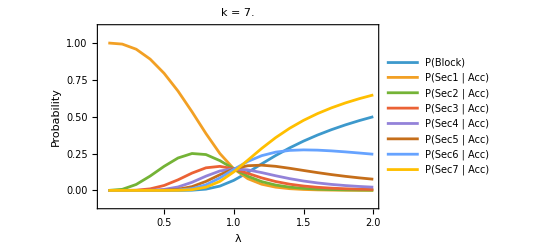

k = 7.5

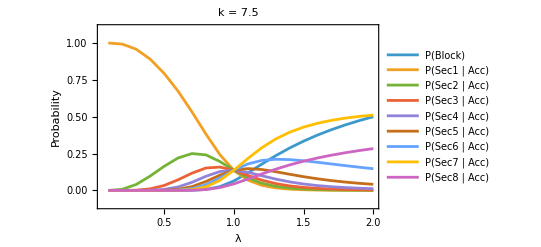

k = 8.

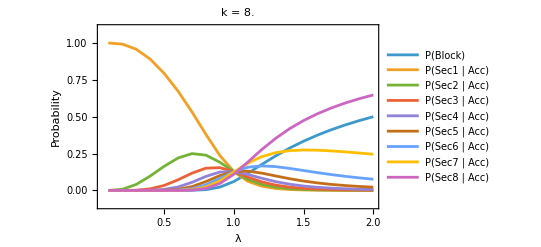

k = 8.5

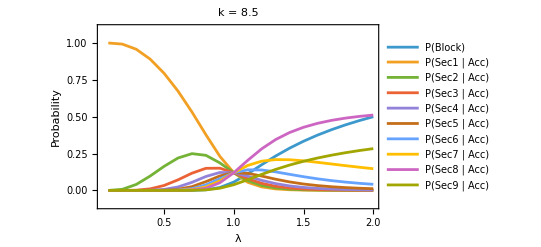

k = 9.

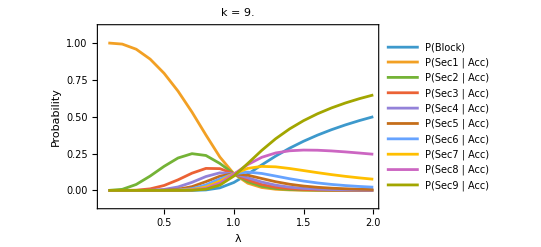

k = 9.5

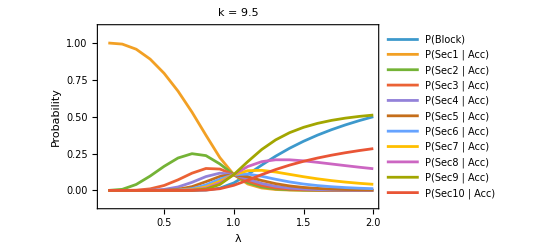

k = 10.

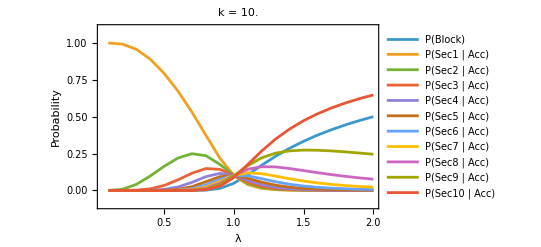

```mathematica
lambdaList = Range[0.1, 2.0, 0.1];
n = 176;
kList = Range[0.5, 10, 0.5]

Do[
 Module[{results, header, rows, fileTag, cap, nSections, plt, curves, legends},
  
  results = bulkServiceResultsCap[lambdaList, n, k];
  
  If[results === $Failed, Continue[]];
  
  Print["k = ", k];
  Print[Dataset[results]];
  
  cap = Round[k n];
  nSections = Ceiling[cap/n];
  
  curves = Join[
    {results[[All, "P(Block)"]]},
    Table[
     results[[All, "P(Sec" <> ToString[j] <> " | Acc)"]],
     {j, 1, nSections}
    ]
   ];
  
  legends = Join[
    {"P(Block)"},
    Table["P(Sec" <> ToString[j] <> " | Acc)", {j, 1, nSections}]
   ];
  
  plt = ListLinePlot[
    curves,
    PlotLegends -> legends,
    DataRange -> {First[lambdaList], Last[lambdaList]},
    PlotRange -> {All, {-0.1, 1.1}},
    Frame -> True,
    FrameLabel -> {"λ", "Probability"},
    PlotLabel -> "k = " <> ToString[k]
   ];
  
  Print[plt];
  
  header = Keys[results[[1]]];
  rows = results /. a_Association :> Values[a];
  
  fileTag = StringReplace[ToString[k], "." -> "p"];
  
  Export[
   "bulkServiceResultsCap_k" <> fileTag <> "_N" <> ToString[n] <> ".csv",
   Prepend[rows, header],
   "CSV"
  ];
  
  Export[
   "bulkServiceResultsCap_k" <> fileTag <> "_N" <> ToString[n] <> ".png",
   plt
  ];
 ],
 {k, kList}
]
```